# Yohan Lee Lab 9

## Examples

```mathematica
SumConvergence[x^n,n]
```

Abs[x]<1

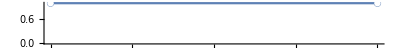

```mathematica
NumberLinePlot[SumConvergence[x^n,n],x]
```

```mathematica
Sum[x^n,{n,0,Infinity}]
```

1/(1-x)

```mathematica
s4[x_]:=Sum[x^n,{n,0,4}]
```

```mathematica
Function[x,∑_(n=0)^4 x^n]
```

Function[x,∑_(n=0)^4 x^n]

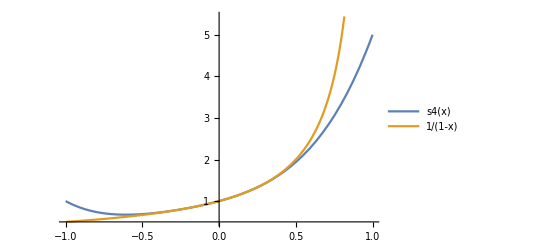

```mathematica
Plot[{s4[x],1/(1-x)},{x,-1,1},PlotLegends->"Expressions"]
```

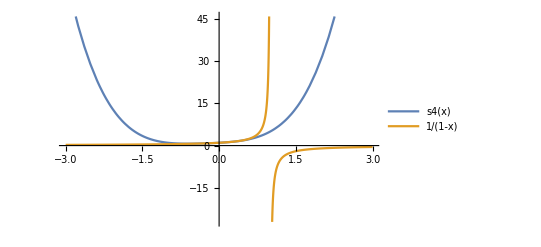

```mathematica
Plot[{s4[x],1/(1-x)},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
s16[x_]:=Sum[x^n,{n,0,16}]
```

```mathematica
Function[x,∑_(n=0)^16 x^n]
```

Function[x,∑_(n=0)^16 x^n]

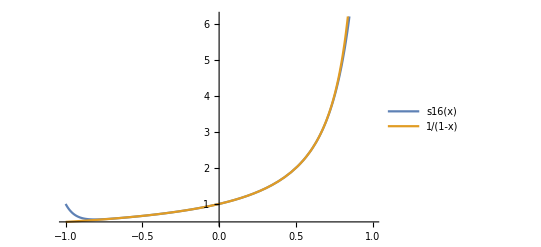

```mathematica
Plot[{s16[x],1/(1-x)},{x,-1,1},PlotLegends->"Expressions"]
```

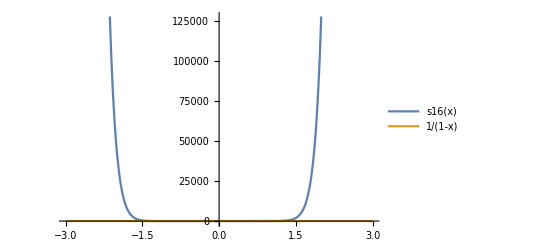

```mathematica
Plot[{s16[x],1/(1-x)},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
Series[Log[5-x],{x,0,5}]
```

Log[5]-x/5-x^2/50-x^3/375-x^4/2500-x^5/15625+O[x]^6

```mathematica
logSeries[x_]:=Log[5]-x/5-x^2/50-x^3/375
```

```mathematica
Function[x,Log[5]-x/5-x^2/50-x^3/375]
```

Function[x,Log[5]-x/5-x^2/50-x^3/375]

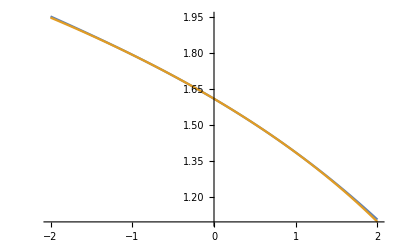

```mathematica
Plot[{logSeries[x],Log[5-x]},{x,-2,2}]
```

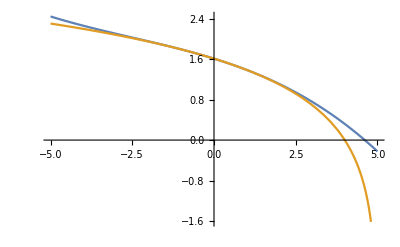

```mathematica
Plot[{logSeries[x],Log[5-x]},{x,-5,5}]
```

```mathematica
NumberLinePlot[SumConvergence[x^n/(n*5^n),n],x]
```

-Graphics-

## Questions

### Q1)

```mathematica
Sum[(-1)^n*x^(2n)/Factorial[2n],{n,0,Infinity}]
```

Cos[x]

```mathematica
SumConvergence[(-1)^n*x^(2n)/Factorial[2n],n]
```

True

The domain of Cos is all real numbers.

```mathematica
sum4[x_]:=Sum[(-1)^n*x^(2n)/Factorial[2n],{n,0,4}]
```

```mathematica
Function[x,∑_(n=0)^4 ((-1)^n x^(2 n))/((2 n)!)]
```

Function[x,∑_(n=0)^4 ((-1)^n x^(2 n))/((2 n)!)]

```mathematica
sum16[x_]:=Sum[(-1)^n*x^(2n)/Factorial[2n],{n,0,16}]
```

```mathematica
Function[x,∑_(n=0)^16 ((-1)^n x^(2 n))/((2 n)!)]
```

Function[x,∑_(n=0)^16 ((-1)^n x^(2 n))/((2 n)!)]

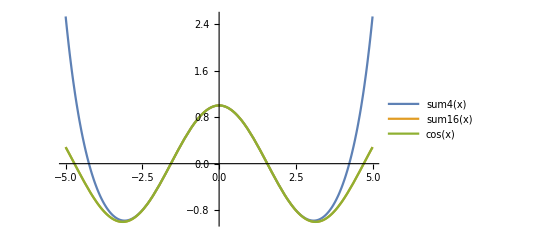

```mathematica
Plot[{sum4[x],sum16[x],Cos[x]},{x,-5,5},PlotLegends->"Expressions"]
```

### Q2)

#### a)

```mathematica
Sum[(-1)^(n-1)*x^n/n,{n,1,Infinity}]
```

Log[1+x]

```mathematica
SumConvergence[(-1)^(n-1)*x^n/n,n]
```

Abs[x]<1

```mathematica
NumberLinePlot[SumConvergence[(-1)^(n-1)*x^n/n,n],x]
```

-Graphics-

#### b)

```mathematica
Sum[(-1)^n(3x)^(2n+1)/Factorial[2n+1],{n,0,Infinity}]
```

Sin[3 x]

```mathematica
SumConvergence[(-1)^n(3x)^(2n+1)/Factorial[2n+1],n]
```

True

Domain is all real numbers.

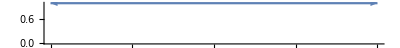

```mathematica
NumberLinePlot[SumConvergence[(-1)^n(3x)^(2n+1)/Factorial[2n+1],n],x]
```

#### c)

```mathematica
Sum[8(n+1)x^n,{n,0,Infinity}]
```

8/(-1+x)^2

```mathematica
SumConvergence[8(n+1)x^n,n]
```

Abs[x]<1

```mathematica
NumberLinePlot[SumConvergence[8(n+1)x^n,n],x]
```

-Graphics-